```mathematica
numericalCutOffV=1.;
numericalCutOffu0I=10.;
numericalCutOffu0II=10.; (*cut off in multiples of b+k*)
(*w=1*)
q[v_]:=0.5*Erfc[v/(√2)];
(*Int*)
g1Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[(beta-(k+b-w x)x/w) Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g2Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[(k+b-w x)^2 Exp[-x^2/2.]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g3Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[(beta^2+(x^2-1)/w^2(k+b-w x)^2-(2beta x)/w(k+b-w x)) Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
betaSolution[b_, k_, nd_, ns_, ndR_, w_]:=y/.FindRoot[g2Int[b, k, nd, ns, ndR, y, w]-2g1Int[b, k, nd, ns, ndR, y, w]+g3Int[b, k, nd, ns, ndR, y, w]/ns , {y, 0.0, 100.}, Method->"Brent"];
f1Int[b_, k_, nd_, ndR_, ns_, beta_, w_, t_]:=Exp[(-g1Int[b, k, nd, ns, ndR, beta, w]t)/(1.  ns)];
f2Int[b_, k_, nd_, ndR_, ns_, beta_, w_, t_]:=Exp[(-g2Int[b, k, nd, ns, ndR, beta, w]t)/(1.  ns)];
puu0[u_, u0_, f1_, f2_]:=Sqrt[1/(2. π (1-f2+u0^2(f2-f1^2)))]Exp[(-(u-u0 f1)^2)/(2(1-f2+u0^2(f2-f1^2)))];
(***************************************************************************************************************************)
(*z=ReLU(u-b)*)
(*expectation value of z with initial overlap u0*)
expzu0[b_, f1_, f2_, u0_]:=(ⅇ^((-(b- u0 f1)^2)/(2 (1-f2+u0^2(f2-f1^2)))) √(1-f2+u0^2(f2-f1^2)))/(√(2. π))-0.5(b-u0 f1) Erfc[(b-u0 f1)/(√(2(1-f2+u0^2(f2-f1^2))))];
(*expectation value of z^2 with initial overlap u0*)
expz2u0[b_, f1_, f2_, u0_]:=(ⅇ^((-(b-u0 f1)^2)/(2 (1-f2+u0^2(f2-f1^2)))) √(1-f2+u0^2(f2-f1^2)) (-b+u0 f1))/(√(2. π))+0.5 ((1-f2+u0^2(f2-f1^2))+(b-u0 f1)^2) Erfc[(b-u0 f1)/(√(2(1-f2+u0^2(f2-f1^2))))];
(*The probability that z is 0*)
au0[b_, f1_, f2_, u0_]:= 0.5+0.5*Erf[(b-u0 f1)/(√(2(1-f2+u0^2(f2-f1^2))))];
(*---------------------Part I begin-----------------------------------*)
(*Part I: average over initial overlap u0 given that the dendrite is not picked for update.*)
(* eqn (12) in note2.pdf*)
(*the dendrite with overlap v is picked for update*)
pLeftMarginI[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/(√(2 π))(1-qv)^(nd-1)(∏_(m=1)^(Rnd-1) qv/(1-qv)*(nd-m)/(Rnd -m));(*qv should always be q[v]*)
(*the dendrite with overlap v is not picked for update*)
pLeftMarginII[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/(√(2 π))(1-qv)^(nd-1)(∏_(m=1)^Rnd qv/(1-qv)*(nd-m)/(Rnd -m+1));(*qv should always be q[v]*)
(*Below is the averge of E[z], E[z^2], and Log(a). There are two definitions for each quantity, they are equivalent, the first one is faster, the second one might be more accurate.*)
expzI[b_, k_, f1_, f2_, nd_, ndR_]:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expzu0[b, f1, f2, u0], {v, -numericalCutOffV(b+k), (b+k)}, {u0, -numericalCutOffu0I(b+k), v}];
expz2I[b_, k_, f1_, f2_, nd_, ndR_]:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) expz2u0[b, f1, f2, u0], {v, -numericalCutOffV(b+k), (b+k)}, {u0, -numericalCutOffu0I(b+k), v}];
expzzI[b_, k_, f1_,f2_,  nd_, ndR_]:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]](NIntegrate[expzu0[b, f1, f2, u0]Exp[-u0^2/2], {u0, -numericalCutOffu0I(b+k), v}]/((1.-q[v])Sqrt[2Pi]))^2, {v, -numericalCutOffV(b+k), (b+k)}];

aI[b_, k_, f1_, f2_, nd_, ndR_]:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]] Exp[-u0^2/2.]/((1-q[v])√(2π)) au0[b, f1, f2, u0], {v, -numericalCutOffV(b+k), (b+k)}, {u0, -numericalCutOffu0I(b+k), v}];
(*---------------------Part I end-----------------------------------*)


(*---------------------Part II begin-----------------------------------*)
(*expectation value of z and z^2 given that the dendrite is updated at t=0. 
Note: for simplicity,    we do not consider the possibility that a dendrite is picked for update but not updated because its overlap is already above b+k*)
expzII[b_, f1_, f2_, k_, ns_, nd_, ndR_]:=expzu0[b, f1, f2, b+k];
expz2II[b_, f1_,f2_,  k_, ns_, nd_, ndR_]:=expz2u0[b, f1, f2, b+k];
aII[b_, f1_, f2_, k_, ns_, nd_, ndR_]:=au0[b, f1, f2, b+k];
(*same as above, but condider the possibility that .......*)
expzII[b_, f1_, f2_, k_, ns_, nd_, ndR_]:=NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expzu0[b, f1, f2, b+k-(beta u0)/ns], {v, -numericalCutOffV(b+k), (b+k)}, {u0, v,b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expzu0[b, f1, f2, u0], {u0, b+k, numericalCutOffu0II(b+k)}];
expz2II[b_, f1_, f2_, k_, ns_, nd_, ndR_]:=NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])expz2u0[b, f1, f2, b+k-(beta u0)/ns], {v, -numericalCutOffV(b+k), (b+k)}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)expz2u0[b, f1, f2, u0], {u0, b+k, numericalCutOffu0II(b+k)}];
expzzII[b_, f1_, f2_, k_, ns_, nd_, ndR_]:=NIntegrate[pLeftMarginII[v, nd, ndR, q[v]](1/(q[v]Sqrt[2.Pi])(NIntegrate[expzu0[b, f1, f2, b+k-(beta u0)/ns]Exp[-u0^2/2], {u0,v, b+k}]+NIntegrate[expzu0[b, f1, f2, u0]Exp[-u0^2/2], {u0,b+k, numericalCutOffu0II(b+k)}]))^2, {v, -numericalCutOffV(b+k), (b+k)}];
aII[b_, f1_, f2_, k_, ns_, nd_, ndR_]:=NIntegrate[pLeftMarginII[v, nd, ndR, q[v]] Exp[-u0^2/2]/(√(2π) q[v])au0[b, f1, f2,  b+k-(beta u0)/ns],{v, -numericalCutOffV(b+k),(b+k)}, {u0, v, b+k}]+NIntegrate[Exp[-u0^2/2]/(√(2π) ndR/nd)au0[b, f1, f2, u0], {u0, b+k, numericalCutOffu0II(b+k)}];
(*---------------------Part II end-----------------------------------*)
(***************************************************************************************************************************)
(* Y=∑_(i=1)^n zi, logA=∑_(i=1)^n loga *)
expYI[b_, k_, f1_, f2_, nd_, ndR_]:=(nd-ndR)expzI[b, k, f1, f2, nd, ndR];
expY2I[b_, k_, f1_, f2_, nd_, ndR_]:=(nd-ndR)(nd-ndR-1)expzzI[b, k, f1, f2, nd, ndR] + (nd-ndR)expz2I[b,k, f1, f2, nd, ndR];
(*AI[b_, f1_, f2_, nd_, ndR_]:=aI[b, f1, f2, nd, ndR]^(nd-ndR);*)
AI[b_, k_, f1_, f2_, nd_, ndR_]:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]](NIntegrate[au0[b, f1, f2, u0]Exp[-u0^2/2], {u0, -numericalCutOffu0I(b+k), v}]/((1.-q[v])Sqrt[2Pi]))^(nd-ndR), {v, -numericalCutOffV(b+k), (b+k)}];
expYII[b_, f1_, f2_, k_, ns_, nd_, ndR_]:=ndR expzII[b, f1, f2, k, ns, nd, ndR];
expY2II[b_, f1_, f2_, k_, ns_, nd_, ndR_]:=ndR(ndR-1)expzzII[b, f1, f2, k, ns, nd, ndR]+ ndR expz2II[b, f1, f2, k, ns, nd, ndR];
(*AII[b_, f1_, f2_, k_, ns_, nd_, ndR_]:=aII[b, f1, f2, k, ns, nd, ndR]^ndR;*)
AII[b_, f1_, f2_, k_, ns_, nd_, ndR_]:=NIntegrate[pLeftMarginII[v, nd, ndR, q[v]](1/(q[v]Sqrt[2Pi])(NIntegrate[au0[b, f1, f2, b+k-(beta u0)/ns]Exp[-u0^2/2], {u0,v, b+k}]+NIntegrate[au0[b, f1, f2, u0]Exp[-u0^2/2], {u0,b+k, numericalCutOffu0II(b+k)}]))^ndR, {v, -numericalCutOffV(b+k), (b+k)}];;
expYSteady[b_, k_, nd_, ndR_]:=nd expzI[b, k, 0., 0., nd, ndR];
expY2Steady[b_, k_, nd_, ndR_]:=nd(nd-1)expzI[b, k, 0., 0., nd, ndR]^2 + nd expz2I[b, k, 0., 0., nd, ndR];
ASteady[b_, k_, nd_, ndR_]:=aI[b, k, 0., 0., nd, ndR]^nd;
(***************************************************************************************************************************)
(*The ansatz of P(Y) is P(Y)=Aδ(Y)+(1-A)/(√(π/2)σ(1+Erf[μ/(√2 σ)]))Exp[(-(Y-μ)^2)/(2 σ^2)]θ(Y). 
μ and σ can be obtained from the following two equations: 
E[Y]/σ=(1-A)h[μ/σ];  E[Y^2]/σ^2=(1-A)(1+μ/σ h[μ/σ]). 
h[x] is defined below. 
*)
h[x_]:=x+Exp[-x^2/2.]/(√(π/2.)(1+Erf[x/(√2)]));
ansatzMuOverSigma[expY_, expY2_, A_]:=x/.FindRoot[((1-A)expY2)/expY^2 h[x]^2==1+x h[x], {x, 100.}];
ansatzSigma[expY_, expY2_, A_, muOverSigma_]:=expY/((1-A)h[muOverSigma]);
ansatzMu[muOverSigma_, sigma_]:=muOverSigma*sigma;
ansatzProbY[Y_, mu_, sigma_, A_]:=A DiracDelta[Y] + (1-A)/(√(π/2)sigma(1+Erf[mu/(√2 sigma)]))Exp[(-(Y-mu)^2)/(2 sigma^2)]HeavisideTheta[Y];
probY[Y_, muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=1.*AI*AII DiracDelta[Y] + (AI(1-AII))/(√(π/2)sigmaII(1+Erf[muII/(√2 sigmaII)]))Exp[(-(Y-muII)^2)/(2 sigmaII^2)]HeavisideTheta[Y]+ (AII(1-AI))/(√(π/2)sigmaI(1+Erf[muI/(√2 sigmaI)]))Exp[(-(Y-muI)^2)/(2 sigmaI^2)]HeavisideTheta[Y]+((1-AI)(1-AII)ⅇ^(-(muI+muII-Y)^2/(2 (sigmaI^2+sigmaII^2))))/(√(π/2)√(sigmaI^2+sigmaII^2))(Erf[(muII sigmaI^2+sigmaII^2 (-muI+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]+Erf[(muI sigmaII^2+sigmaI^2 (-muII+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))])/((1+Erf[muI/(√2 sigmaI)])(1+Erf[muII/(√2 sigmaII)]));
falseNegative[th_, muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=1-(AI(1-AII)(1+Erf[(muII-th)/(√2 sigmaII)]))/(1+Erf[muII/(√2 sigmaII)])-(AII(1-AI)(1+Erf[(muI-th)/(√2 sigmaI)]))/(1+Erf[muI/(√2 sigmaI)])-((1-AI)(1-AII))/(√(π/2)√(sigmaI^2+sigmaII^2)(1+Erf[muI/(√2 sigmaI)])(1+Erf[muII/(√2 sigmaII)]))NIntegrate[ⅇ^(-(muI+muII-Y)^2/(2 (sigmaI^2+sigmaII^2)))(Erf[(muII sigmaI^2+sigmaII^2 (-muI+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]+Erf[(muI sigmaII^2+sigmaI^2 (-muII+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]), {Y, th, Infinity}];
Y99Lower[muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=If[AI AII>=0.01, 0, th/.FindRoot[falseNegative[th, muI, sigmaI, AI, muII, sigmaII, AII]==0.01, {th, 0, b+k}, Method->"Brent"]];
Y99Upper[muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=th/.FindRoot[falseNegative[th, muI, sigmaI, AI, muII, sigmaII, AII]==0.99, {th, 0, 5*(b+k)}, Method->"Brent"];
YMean[muI_, sigmaI_, AI_, muII_, sigmaII_, AII_]:=AI (1.-AII) (muII-(ⅇ^(-muII^2/(2 sigmaII^2)) √(2/π) sigmaII)/(-2+Erfc[muII/(√2 sigmaII)]))+ AII(1.-AI) (muI-(ⅇ^(-muI^2/(2 sigmaI^2)) √(2/π) sigmaI)/(-2+Erfc[muI/(√2 sigmaI)]))+((1-AI)(1-AII))/(√(π/2)√(sigmaI^2+sigmaII^2))1./((1+Erf[muI/(√2 sigmaI)])(1+Erf[muII/(√2 sigmaII)]))NIntegrate[ⅇ^(-(muI+muII-Y)^2/(2 (sigmaI^2+sigmaII^2)))(Erf[(muII sigmaI^2+sigmaII^2 (-muI+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))]+Erf[(muI sigmaII^2+sigmaI^2 (-muII+Y))/(√2 sigmaI sigmaII √(sigmaI^2+sigmaII^2))])Y, {Y, 0, Infinity}]
(***************************************************************************************************************************)
```

```mathematica
nd=200; ns=300; b=2.75;k=2.25;ndR=4;
beta=betaSolution[b, k, nd, ns, ndR, 1.]//Quiet;
expYSteadyVar=expYSteady[b, nd, ndR];
expY2SteadyVar=expY2Steady[b, nd, ndR];
ASteadyVar=ASteady[b, nd, ndR];
muOverSigmaSteadyVar=ansatzMuOverSigma[expYSteadyVar,expY2SteadyVar,ASteadyVar]//Quiet;
sigmaSteadyVar=ansatzSigma[expYSteadyVar,expY2SteadyVar,ASteadyVar, muOverSigmaSteadyVar];
muSteadyVar = ansatzMu[muOverSigmaSteadyVar, sigmaSteadyVar];
(*Plot[ansatzProbY[Y, muSteadyVar, sigmaSteadyVar, ASteadyVar], {Y, 0.001, 10}, PlotRange->All]*)
th=muSteadyVar-√2 sigmaSteadyVar InverseErf[(0.01(1+Erf[muSteadyVar/(√2 sigmaSteadyVar)]))/(1-ASteadyVar)-1]//Quiet;
(*Plot[g1Int[b, k, nd, ns, ndR, beta, Sqrt[w2]], {w2, 0.95^2, 1.05^2}, AxesLabel->{"w^2", "g1(w)"}]
Plot[g2Int[b, k, nd, ns, ndR, beta, Sqrt[w2]], {w2, 0.95^2, 1.05^2}, AxesLabel->{"w^2", "g2(w)"}]
Plot[Sqrt[g2Int[b, k, nd, ns, ndR, beta, w]/ns]/w, {w, 0.95, 1.05}, AxesLabel->{"w^2", "g3(w)"}]*)
```

```mathematica
ndList={400}; bList={2.5, 2.75, 3.0};kList={2.0, 2.25, 2.5, 2.75, 3.0};ndRList={2, 3, 4};
paramList = Table[{nd, 60000/nd, b, k, ndR}, {nd, ndList}, {b, bList}, {k, kList}, {ndR, ndRList}];
paramList = ArrayReshape[paramList, {Length[ndList]*Length[bList]*Length[kList]*Length[ndRList],5}];
tmpFun[nd_, ns_, b_, k_, ndR_]:={nd, ns, b, k, ndR, betaSolution[b, k, nd, ns, ndR, 1.]}
betaList = MapThread[tmpFun, Transpose[paramList]]//Quiet;
```

```mathematica
Export["beta_list.txt", betaList,"Table","FieldSeparators"->" " ]
```

beta_list.txt

```mathematica
tStart=900; tEnd=1200;tStep=100;
tList=Table[t, {t, tStart, tEnd, tStep}];
f1List=Thread[f1Int[b, k, nd, ndR, ns, beta, 1., tList]];
f2List=Thread[f2Int[b, k, nd, ndR, ns, beta, 1., tList]];
expYIList=Thread[expYI[b, f1List, f2List, nd, ndR]];
expY2IList=Thread[expY2I[b, f1List, f2List, nd, ndR]];
AIList=Thread[AI[b, f1List, f2List, nd, ndR]];
expYIIList=Thread[expYII[b, f1List, f2List, k, ns,nd, ndR]];
expY2IIList=Thread[expY2II[b, f1List, f2List, k, ns, nd, ndR]];
AIIList=Thread[AII[b, f1List, f2List, k, ns, nd, ndR]];
muOverSigmaIList=MapThread[ansatzMuOverSigma, {expYIList,expY2IList, AIList}]//Quiet;
sigmaIList=Thread[ansatzSigma[expYIList,expY2IList, AIList, muOverSigmaIList]];
muIList=Thread[ansatzMu[sigmaIList, muOverSigmaIList]];
muOverSigmaIIList=MapThread[ansatzMuOverSigma, {expYIIList,expY2IIList, AIIList}]//Quiet;
sigmaIIList=Thread[ansatzSigma[expYIIList,expY2IList, AIIList, muOverSigmaIIList]];
muIIList=Thread[ansatzMu[sigmaIIList, muOverSigmaIIList]];
falseNegativeList=Thread[falseNegative[th, muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList]];
Y99LowerList=MapThread[Y99Lower,{ muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList}]//Quiet;
Y99UpperList=MapThread[Y99Upper,{ muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList}]//Quiet;
YMeanList=MapThread[YMean,{ muIList, sigmaIList, AIList, muIIList, sigmaIIList, AIIList}]//Quiet;
```

NIntegrate::nlim: u0 = v is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: u0 = v is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
Y99LowerList
```

{2.22581,1.79678,1.41174,1.07614}

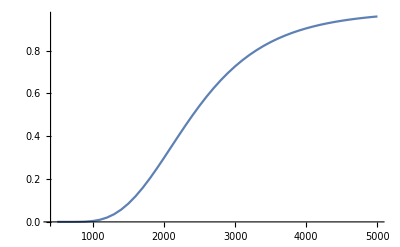

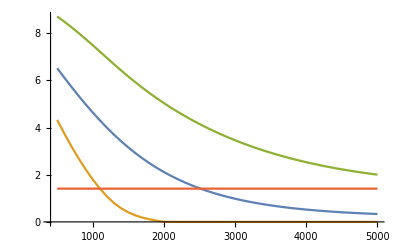

```mathematica
fnTimeList=Transpose[{tList, falseNegativeList}];
meanTimeList=Transpose[{tList, YMeanList}];
lower99TimeList= Transpose[{tList, Y99LowerList}];
upper99TimeList=Transpose[{tList, Y99UpperList}];
ListLinePlot[fnTimeList, PlotRange->All]
ListLinePlot[{meanTimeList, lower99TimeList,upper99TimeList, Table[{t, th}, {t, tList}]}, PlotRange->All]
```

```mathematica
Export["meanTimeList.csv",meanTimeList,"CSV"];
Export["lower99TimeList.csv",lower99TimeList,"CSV"];
Export["upper99TimeList.csv",upper99TimeList,"CSV"];
```

```mathematica
tmpFun1[Y_, mu_, sigma_, A_]:=(1-A)/(√(π/2)sigma(1+Erf[mu/(√2 sigma)]))Exp[(-(Y-mu)^2)/(2 sigma^2)];
```

1000

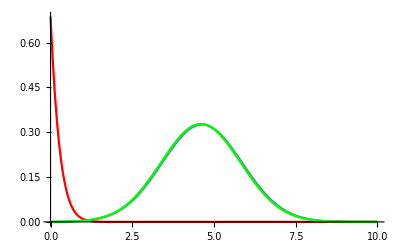

```mathematica
idx=2;
tList[[idx]]
Show[Plot[probY[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]], muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]], {Y, 0, 10}, PlotRange->All],
Plot[tmpFun1[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]]], {Y, 0, 10}, PlotRange->All, PlotStyle->Red],Plot[tmpFun1[Y, muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]], {Y, 0, 10}, PlotRange->All, PlotStyle->Green]
]
(*Plot[Table[probY[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]], muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]], {idx, 1, 30, 3}], {Y, 0, 10}, PlotRange->All]*)
```

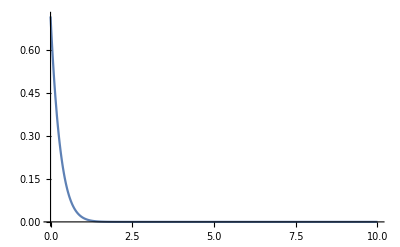

```mathematica
probYSingle[Y_, muI_, sigmaI_, AI_]:=1.*AI*AII DiracDelta[Y] + (1-AI)/(√(π/2)sigmaI(1+Erf[muI/(√2 sigmaI)]))Exp[(-(Y-muI)^2)/(2 sigmaI^2)]HeavisideTheta[Y];
Plot[probYSingle[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]]], {Y, 0, 10}, PlotRange->All]
```

```mathematica
tList[[7]]
```

1100

```mathematica
idx=9;
YProbList= Table[{Y, probY[Y, muIList[[idx]], sigmaIList[[idx]], AIList[[idx]], muIIList[[idx]], sigmaIIList[[idx]], AIIList[[idx]]]}, {Y, 0.1, 8, 0.1}];
Export["YProbList.csv",YProbList,"CSV"];
```

```mathematica
pLeftMarginI[v_, nd_, Rnd_, qv_]:=(nd  Exp[-v^2/2])/(√(2 π))(1-qv)^(nd-1)(∏_(m=1)^(Rnd-1) qv/(1-qv)*(nd-m)/(Rnd -m));(*qv should always be q[v]*)
expzzI[b_, k_, f1_,f2_,  nd_, ndR_]:=NIntegrate[pLeftMarginI[v, nd, ndR, q[v]](NIntegrate[expzu0[b, f1, f2, u0]Exp[-u0^2/2], {u0,-Infinity, v}]/((1.-q[v])Sqrt[2.Pi]))^2, {v, -b-k, b+k}];
```

```mathematica
expzzI[b, f1List[[idx]],f2List[[idx]],  nd, ndR]
```

NIntegrate::nlim: u0 = v is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.01253×10^-7

```mathematica
NIntegrate[expzu0[2.75,0.7362027095583606,0.5428554947562438,u0] Exp[-u0^2/2],{u0,-∞,(b+k)}]
```

0.00228815